{{vc→(c r v0)/(1+c r s)}}

{ⅇ^(-t/(c r)) v0}

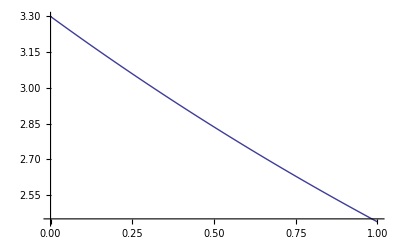

```mathematica
soln=Solve[c v0-vc/(1/(s c))-vc/r==0,vc]
soln'=InverseLaplaceTransform[vc/.soln2,s,t]
(*soln=DSolve[{vc[t]+r i[t]==0,i[t]==c vc'[t],vc[0]==v0},{vc,i},t]*)
With[{f=soln'/.{v0->3.3,c->10*^-6,r->330*^3}},
(*Refine[Solve[vc[t]==v/.soln,t,Reals],Assumptions->v>0]/.conditions*)
Plot[f,{t,0,1}]]
```

{{vc→(r (c rs s v0+vs))/(s (r+rs+c r rs s)),is→-(c r s v0-vs-c r s vs)/(s (r+rs+c r rs s))}}

{(ⅇ^(-((r+rs) t)/(c r rs)) (r v0+rs v0-r vs+ⅇ^(((r+rs) t)/(c r rs)) r vs))/(r+rs)}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→0.00138831}}

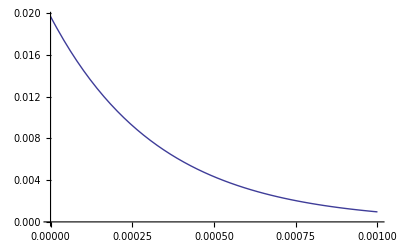

```mathematica
Clear[vc3]
Clear[is3]
soln3=Solve[is-vc/(1/(s c))-vc/r+c v0==0&&is==(vs/s-vc)/rs,{vc, is}]
cond3=Dispatch[{vs->3.3,c->10*^-6,r->330*^3,rs->33,v0->2.65}];
vctmp=InverseLaplaceTransform[vc/.soln3,s,t]
vc3[tx_]:=vctmp[[1]]/.cond3/.t->tx
is3[tx_]:=((vs-vc3[t])/rs)/.cond3/.t->tx
NSolve[vc3[t]==3.29 ,t, Reals]
Plot[is3[t],{t,0,0.001}]
(*Solve[soln3a[[1]]/.cond3==3.29,t]*)
```

```mathematica
is3[0.0001]
```

0.0000395086

```mathematica
vctmp[[1]]/.cond3/.t->0
```

2.65

```mathematica
soln4=Solve[0.5==3.3(1-ⅇ^(-t/(r c))),r]
r/.soln4/.{t->0.5,c->10*^-6}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{r→(6.08631 t)/c}}

{304316.}